```mathematica
Integrate[Sign[G]/(G+π),{G,-π,t}]
```

If[t∈Reals,(-1+2 HeavisideTheta[t]) Log[(π+t)/π],Integrate[Sign[G]/(G+π),{G,-π,t},Assumptions→t∉Reals]]

```mathematica
g[t_]:=(-1+2 HeavisideTheta[t]) Log[(π+t)/π]
```

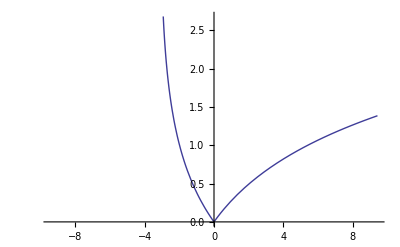

```mathematica
Plot[g[t],{t,-3π,3π} ]
```

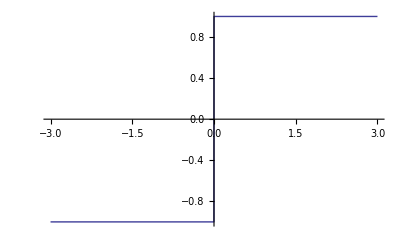

```mathematica
Plot[-1+2 HeavisideTheta[t],{t,-3,3}]
```

```mathematica
D[g[t],t]
```

(-1+2 HeavisideTheta[t])/(π+t)+2 DiracDelta[t] Log[(π+t)/π]

```mathematica
D[(-1+2 HeavisideTheta[t])/(π+t),t]
```

(2 DiracDelta[t])/(π+t)-(-1+2 HeavisideTheta[t])/(π+t)^2

```mathematica
D[ HeavisideTheta[t],t]
```

DiracDelta[t]